```mathematica
g[m_]:=(2.2*10^3*m^0.306)^-4.38+1.3*10^-9*(m+10^11*m^2+10^27*m^4)^-0.36+1.3*10^-16*(m+10^6*m^2)^-0.85
F[x_,m_,s_,rho_]:=6/(Pi*rho*s*Sqrt[2*Pi])*Erfc[(Log[x]-m+3*s^3)/(Sqrt[2]*s)]*Exp[-3*m+9*s^2/2]
```

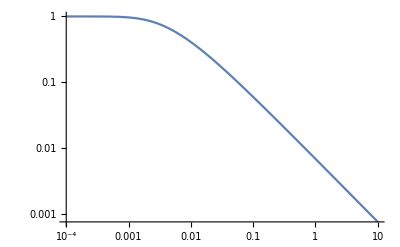

```mathematica
rho=3;
LogLogPlot[{(NIntegrate[D[-g[4/3*Pi*rho*(a/2)^3/1000],a]*(F[z*10,-2.649,1.786,rho]-F[a*10,-2.649,1.786,rho]),{a,z,100}]-NIntegrate[D[-g[4/3*Pi*rho*(a/2)^3/1000],a]*(F[(z+0.001)*10,-2.649,1.786,rho]-F[a*10,-2.649,1.786,rho]),{a,z,100}])/F[z*10,-2.649,1.786,rho]/g[4/3*Pi*rho*(z/2)^3/1000]},{z,0.0001,10},PlotLegends->"Expressions"]
```

```mathematica
(NIntegrate[D[-g[4/3*Pi*rho*(a/2)^3/1000],a]*(F[z*10,-2.649,1.786,rho]-F[a*10,-2.649,1.786,rho]),{a,z,100}]-NIntegrate[D[-g[4/3*Pi*rho*(a/2)^3/1000],a]*(F[(z+0.001)*10,-2.649,1.786,rho]-F[a*10,-2.649,1.786,rho]),{a,z,100}])/F[z*10,-2.649,1.786,rho]/g[4/3*Pi*rho*(z/2)^3/1000]/.z->1.853
```

NIntegrate::nlim: a = z is not a valid limit of integration.

0.453511

```mathematica
LogLogPlot[{D[Integrate[D[-g[4/3*Pi*rho*(a/2)^3/1000],a]*(F[z*10,-2.649,1.786,rho]-F[a*10,-2.649,1.786,rho]),{a,z,1000}],z]},{z,0.0086,1.853},PlotLegends->"Expressions"]
```

General::ivar: 0.00860094 is not a valid variable.

$Aborted